# Spectral Lags in Very High Energy Emission of GRBs

## Model

### Parameters

```mathematica
universe={Hobs_,Ωm_};
```

```mathematica
population={density0_,index_,zc_};
```

```mathematica
burst={γ_,η0_,r0_,n_,ω0_,θ0_,k_,α_};
```

```mathematica
observer={detectorArea_,z_,χ_};
```

### Relativity

```mathematica
v[γ_]:=√(1-1/γ^2);
```

### Cosmology

```mathematica
ΩΛ[Ωm_]:=1-Ωm;
```

```mathematica
distance[universe,z_]:=1/Hobs √(1/ΩΛ[Ωm])((1+z)Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm](1+z)^3]-Hypergeometric2F1[1/3,1/2,4/3,-Ωm/ΩΛ[Ωm]]);
```

```mathematica
photonSphereArea[universe_,z_]:=4π distance[universe,z]^2;
```

```mathematica
burstsSphereArea[universe_,z_]:=(4π distance[universe,z]^2)/(1+z)^2;
```

```mathematica
shellVolumePerRedshift[universe,z_]:=(4π distance[{Hobs,Ωm},z]^2)/(1+z)^3 1/(Hobs √(Ωm(1+z)^3+ΩΛ[Ωm]));
```

### Light curve

```mathematica
i[burst,z_,χ_,ω_,θ_,ϕ_]:=
If[ω==∞,
0,
1/(2k)ω(ω/ω0)^α ExpIntegralE[(α+1)/(2k)+1,(θ/θ0)^2(ω/ω0)^(-2k)(v[γ]γ(1+z)(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ]))^(-2k)]
];
```

```mathematica
j[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z))^3 π/(n Sin[(3π)/n]),
τ^3/3 Hypergeometric2F1[1,3/n,(n+3)/n,-(τ/(r0(1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])(1+z)))^n]
];
```

```mathematica
p[universe_,burst,observer,{τ1_,τ2_},{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])(j[burstValues,z,χ,τ2,θ,ϕ]-j[burstValues,z,χ,τ1,θ,ϕ]),{θ,χ,∞},{ϕ,0,π}])
];
```

### Duration

```mathematica
Options[duration]={part->0.99};
duration[universe_,burst,observer,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,observerValues,p∞,precision},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
observerValues={detectorArea,z,χ};
p∞=p[universe,burstValues,observerValues,{0.,∞},{ω1,ω2}];
pi[τ_?NumberQ]:=p[universe,burstValues,observerValues,{0.,τ},{ω1,ω2}];
τ/.FindRoot[pi[τ]-OptionValue[part]p∞,{τ,r0/γ^2(1.+z)}]
];
```

### Stretching factor

```mathematica
jτ[burst,z_,χ_,τ_,θ_,ϕ_]:=
If[τ==∞,
0,
τ^2/(1+((2τ)/(r0 (1+z) (-2+2/v[γ]+θ^2+χ^2-2 θ χ Cos[ϕ])))^n)
];
```

```mathematica
pτ[universe_,burst,observer,τ_,{ω1_,ω2_}]:=Block[{burstValues},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
detectorArea/photonSphereArea[universe,z](2η0)/(v[γ]γ(1+z))^(2-α)(NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,0,χ},{ϕ,0,π}]+NIntegrate[θ/((1/v[γ]-1+θ^2/2+χ^2/2-θ χ Cos[ϕ])^(5-α))(i[burstValues,z,χ,ω2,θ,ϕ]-i[burstValues,z,χ,ω1,θ,ϕ])jτ[burstValues,z,χ,τ,θ,ϕ],{θ,χ,∞},{ϕ,0,π}])
];
```

```mathematica
Options[κ]={δ->0.01,accurateQ->True};
κ[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{p12∞,p23∞,diff,diffτ,δτ,τmiddle,τend,κmin,κmax,minDifference,maxDifference,diffDifference,precision,accQ},
p12∞=p[universe,burst,observer,{0.,∞},{ω1,ω2}];
p23∞=p[universe,burst,observer,{0.,∞},{ω2,ω3}];
diff[τ_?NumberQ,κ_?NumberQ]:=p[universe,burst,observer,{0.,τ},{ω1,ω2}]/(p12∞)-p[universe,burst,observer,{0.,κ τ},{ω2,ω3}]/(p23∞);
diffτ[τ_?NumberQ,κ_?NumberQ]:=pτ[universe,burst,observer,τ,{ω1,ω2}]/(p12∞)-κ pτ[universe,burst,observer,κ τ,{ω2,ω3}]/(p23∞);
accQ=OptionValue[accurateQ];
If[TrueQ[accQ],
τend=duration[universe,burst,observer,{ω1,ω3}];
δτ=OptionValue[δ]τend;
maxDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]>0,
If[diff[τend,κ]>0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,zero-δτ}];
];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
];
minDifference[κ_?NumberQ]:=Block[{zero,derivativeZero},
If[diff[δτ,κ]<0,
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
If[diff[τend,κ]<0,
zero=τ/.FindRoot[diff[τ,κ],{τ,δτ,τend}];
derivativeZero=τ/.FindRoot[diffτ[τ,κ],{τ,zero+δτ,τend}];
{derivativeZero,diff[derivativeZero,κ]},
{0.,0.}
]
]
];
κmin=κ/.FindRoot[diff[δτ,κ],{κ,1.}];
κmax=κ/.FindRoot[diff[τend,κ],{κ,1.}];
diffDifference[κ_?NumberQ]:=maxDifference[κ][[2]]+minDifference[κ][[2]];
κ/.FindRoot[diffDifference[κ],{κ,κmin,κmax}]
,
τmiddle=duration[universe,burst,observer,{ω1,ω3},part->0.5];
κ/.FindRoot[diff[τmiddle,κ],{κ,1.}]
]
];
```

```mathematica
SetSharedFunction[κStoredValues];
Options[κCache]={δ->0.01,accurateQ->True};
κCache[universe_,burst_,observer_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{},
If[Not[NumberQ[κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]]],κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]=κ[universe,burst,observer,{ω1,ω2,ω3},δ->Options[δ],accurateQ->Options[accurateQ]]];
κStoredValues[universe,burst,observer,{ω1,ω2,ω3},OptionValue[δ],OptionValue[accurateQ]]
];
```

```mathematica
κSave[]:=DumpSave["kappa.mx",κStoredValues];
```

```mathematica
κLoad[]:=If[FileExistsQ["kappa.mx"],<<"kappa.mx"];
```

### Total Energy

```mathematica
energy[burst,ω1_]:=(16 π^3)/(3n(-2k-α-2)Sin[(3π)/n])γ^(-2k-α)(1-1/(4 γ^2))η0 r0^3 θ0^2 ω0^(-2k-α)/ω1^(-2k-α-2);
```

### Distribution

```mathematica
Options[zmax]={minParticles->10};
zmax[universe_,burst_,detectorArea_,χ_,{ω1_,ω2_},OptionsPattern[]]:=Block[{int,z1,z2},
int[z_?NumberQ]:=p[universe,burst,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
z1=1;
While[int[z1]<0,z1/=2.];
z2=1;
While[int[z2]>0,z2*=2.];
z/.FindRoot[int[z],{z,z1,z2}]
];
```

```mathematica
Options[χmax]={minParticles->10};
χmax[universe_,burst,detectorArea_,z_,{ω1_,ω2_},OptionsPattern[]]:=Block[{burstValues,int,χ0},
burstValues={γ,η0,r0,n,ω0,θ0,k,α};
int[χ_?NumberQ]:=p[universe,burstValues,{detectorArea,z,χ},{0.,∞},{ω1,ω2}]-OptionValue[minParticles];
If[int[0]<0,
Return[0],
χ0=1/γ;
While[int[χ0]>0,χ0*=2.;];
];
χ/.FindRoot[int[χ],{χ,0,χ0}]
];
```

```mathematica
burstDensity[population,z_]:=density0(1+z)^index Exp[-z/zc];
```

```mathematica
phaseVolume[universe_,population_,{z1_?NumberQ,z2_?NumberQ}]:=NIntegrate[shellVolumePerRedshift[universe,z]burstDensity[population,z],{z,z1,z2}];
```

```mathematica
equiprobableRedshifts[universe_,population_,{z1_,z2_},n_]:=Block[{total,δ,result,print},
total=phaseVolume[universe,population,{z1,z2}];
δ=total/(n-1);
result=ParallelTable[z/.FindRoot[phaseVolume[universe,population,{z1,z}]-vi,{z,z1,z2}],{vi,0,total,δ}];
result
];
```

```mathematica
equiprobableAngles[{χ1_,χ2_},n_]:=Table[√χsqr,{χsqr,χ1^2,χ2^2,(χ2^2-χ1^2)/(n-1)}];
```

```mathematica
Options[κTable]={accurateQ->True};
κTable[universe_,burst_,detectorArea_,zTable_,χTable_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{print,result,c},
κLoad[];
result=Flatten[ParallelTable[{zTable[[iz]],χTable[[iχ]],κCache[universe,burst,{detectorArea,zTable[[iz]],χTable[[iχ]]},{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]]},{iz,1,Length[zTable]},{iχ,1,Length[χTable]}],1];
κSave[];
result
];
```

```mathematica
Options[κDistribution]={accurateQ->True,zn->9,znHR->6000,χn->9,χnHR->6000,zmin->0.1,binCount->1200};
κDistribution[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z2,χ2,κint,χmaxint,κtHR,histogram},
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3}];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3}];

(* Calculating low resolution table *)
Block[{zt,χt,κt,χmaxt},
zt=equiprobableRedshifts[universe,population,{OptionValue[zmin],z2},OptionValue[zn]];
χt=equiprobableAngles[{0,χ2},OptionValue[χn]];
κt=κTable[universe,burst,detectorArea,zt,χt,{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
χmaxt=ParallelTable[{zi,χmax[universe,burst,detectorArea,zi,{ω2,ω3}]},{zi,zt}];
(*κint=Interpolation[κt];*)
χmaxint=Interpolation[χmaxt];
];

κint[z_,χ_]:=0.9+χ/0.01 Exp[-z];

(* Calculating high resolution table *)
Block[{zt,χt},
zt=equiprobableRedshifts[universe,population,{OptionValue[zmin],z2},OptionValue[znHR]];
χt=equiprobableAngles[{0,χ2},OptionValue[χnHR]];
κtHR=Flatten[Table[{zi,χi,κint[zi,χi]},{zi,zt},{χi,χt}],1];
];

(* Calculating histogram *)
Block[{κmin,κmax},
κmin=Min[Table[κi[[3]],{κi,κtHR}]];
κmax=Max[Table[κi[[3]],{κi,κtHR}]];
histogram=Table[{κmin+{it-1,it}/OptionValue[binCount](κmax-κmin),0},{it,1,OptionValue[binCount]}];
Block[{it,bin},For[it=1,it≤Length[κtHR],it++,
bin=Max[Ceiling[(κtHR[[it]][[3]]-κmin)/(κmax-κmin)OptionValue[binCount]],1];
If[κtHR[[it]][[2]]≤χmaxint[κtHR[[it]][[1]]],histogram[[bin]][[2]]+=1];
];];
];

(* Calculating distribution *)
Block[{averagedHistogram,total,interpolation},
averagedHistogram=Table[{Mean[entry[[1]]],entry[[2]]},{entry,histogram}];
interpolation=Interpolation[averagedHistogram];
total=NIntegrate[interpolation[κi],{κi,averagedHistogram[[1]][[1]],averagedHistogram[[Length[averagedHistogram]]][[1]]}];
ProbabilityDistribution[interpolation[κi]/total,{κi,averagedHistogram[[1]][[1]],averagedHistogram[[Length[averagedHistogram]]][[1]]}]
]
];
```

```mathematica
Options[κDistributionAlternate]={accurateQ->True,zn->9,znHR->4000,χn->9,χnHR->4000,zmin->0.1,binCount->400,resolution->20};
κDistributionAlternate[universe_,population_,burst_,detectorArea_,{ω1_,ω2_,ω3_},OptionsPattern[]]:=Block[{z2,χ2,κint,χmaxint,χκ,zκmax,zκmin,int,limit,pdf,κleft,κright,pdfTable,pdfi,norm},
z2=zmax[universe,burst,detectorArea,0,{ω2,ω3}];
χ2=χmax[universe,burst,detectorArea,OptionValue[zmin],{ω2,ω3}];

(* Calculating low resolution table *)
Block[{zt,χt,κt,χmaxt},
zt=equiprobableRedshifts[universe,population,{OptionValue[zmin],z2},OptionValue[zn]];
χt=equiprobableAngles[{0,χ2},OptionValue[χn]];
κt=κTable[universe,burst,detectorArea,zt,χt,{ω1,ω2,ω3},accurateQ->OptionValue[accurateQ]];
χmaxt=ParallelTable[{zi,χmax[universe,burst,detectorArea,zi,{ω2,ω3}]},{zi,zt}];
(*κint=Interpolation[κt];*)
χmaxint=Interpolation[χmaxt];
];

κint[z_,χ_]:=0.9+χ/0.01 Exp[-z];

χκ=InverseFunction[κint,2,2];
zκmax=κint[#,χmaxint[#]]&;
zκmin=κint[#,0.]&;

int[z_?NumberQ,κ_?NumberQ]:=1/2 χκ[z,κ]shellVolumePerRedshift[universe,z]burstDensity[population,z];
limit[κ_?NumberQ]:=If[κ<κint[z2,0.],InverseFunction[zκmin][κ],InverseFunction[zκmax][κ]];
pdf[κ_?NumberQ]:=NIntegrate[int[z,κ],{z,OptionValue[zmin],limit[κ]}];
κleft=κint[OptionValue[zmin],0.];
κright=κint[OptionValue[zmin],χmaxint[OptionValue[zmin]]];
pdfTable=Table[{κi,pdf[κi]},{κi,κleft+(κright-κleft)/OptionValue[resolution],κright-(κright-κleft)/OptionValue[resolution],(κright-κleft)/OptionValue[resolution]}];
PrependTo[pdfTable,{κleft,0}];
AppendTo[pdfTable,{κright,0}];
pdfi=Interpolation[pdfTable];
norm=NIntegrate[pdfi[κi],{κi,κleft,κright}];
ProbabilityDistribution[pdfi[κi]/norm,{κi,κleft,κright}]
];
```

```mathematica
dist=κDistribution[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞},accurateQ->False,zn->33,χn->9];
distAlt=κDistributionAlternate[defaultUniverse[],defaultPopulation[],defaultBurst[],defaultDetectorArea[],{0.1,1.,∞},accurateQ->False,zn->33,χn->9];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in κi near {κi} = {1.1443}. NIntegrate obtained 9028.7 and 0.200092 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

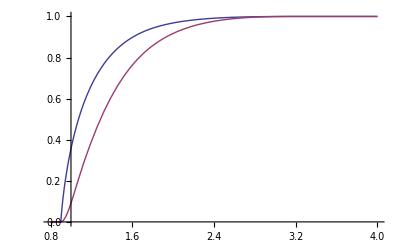

```mathematica
PrintTemporary[Dynamic[κi]];
Plot[{CDF[dist,κi],CDF[distAlt,κi]},{κi,0.8,4}]
```

### Default Parameters

```mathematica
Options[defaultUniverse]={Hobs->2.*^-18,Ωm->0.317};
defaultUniverse[OptionsPattern[]]:={OptionValue[Hobs],OptionValue[Ωm]};
```

```mathematica
Options[defaultPopulation]={density0->0.655427*^-50,index->3,zc->3.};
defaultPopulation[OptionsPattern[]]:={OptionValue[density0],OptionValue[index],OptionValue[zc]};
```

```mathematica
Options[defaultBurst]={γ->100.,η0->1.*^45,r0->2.*^3,n->6,ω0->1.,θ0->2.5*^-5,k->-1,α->-1};
defaultBurst[OptionsPattern[]]:={OptionValue[γ],OptionValue[η0],OptionValue[r0],OptionValue[n],OptionValue[ω0],OptionValue[θ0],OptionValue[k],OptionValue[α]};
```

```mathematica
defaultDetectorArea[]:=5.563*^-18;
```

```mathematica
Options[defaultObserver]={detectorArea->defaultDetectorArea[],z->1.,χ->0.};
defaultObserver[OptionsPattern[]]={OptionValue[detectorArea],OptionValue[z],OptionValue[χ]};
```